```mathematica
Block[{Print},<<xAct`xTensor`]
Block[{Print},<<xAct`xTras`]
Block[{Print},<<xAct`xPert`]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

# Scalar phi^4 theory exact renormalization using the Functional Renormalization Group

Author: Wojciech Śmiałek

## Definitions

### General

```mathematica
DefManifold[M,dim,{μ,ν,ρ,σ,ai,bi,ci,di,ei,fi,gi,hi,ii,ji,ki,li}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
Block[{Print},DefMetric[+1,metric[-μ,-ν],cd,{"|","∂"},PrintAs->"g"]]
$CovDFormat = "Prefix";
(*Wick-rotated space - metric is just a delta*)
```

### Tensors

```mathematica
DefTensor[phi[],M,PrintAs->"ϕ"]
DefTensor[phiP[LI[q]],M,PrintAs->"ϕp"]
DefTensor[momentum[LI[q],-ai],M,PrintAs->"p"]
```

** DefTensor: Defining tensor phi[].

** DefTensor: Defining tensor phiP[LI[q]].

** DefTensor: Defining tensor momentum[LI[q],-ai].

### Functions, constants

```mathematica
DefScalarFunction[momentumSquared,PrintAs->"p^2"]
DefScalarFunction[Regulator, PrintAs->"Rk"]
DefScalarFunction[renormalizationAfunct, PrintAs->"ZA"]
DefScalarFunction[renormalizationHfunct, PrintAs->"Zh"]
```

** DefScalarFunction: Defining scalar function momentumSquared.

** DefScalarFunction: Defining scalar function Regulator.

** DefScalarFunction: Defining scalar function renormalizationAfunct.

** DefScalarFunction: Defining scalar function renormalizationHfunct.

```mathematica
DefConstantSymbol[renormalizationPhi, PrintAs->"Zϕ"]
DefConstantSymbol[renormalizationM, PrintAs->"Zm"]
DefConstantSymbol[renormalizationL, PrintAs->"Zλ"]
DefConstantSymbol[mass, PrintAs->"m"]
DefConstantSymbol[lambda, PrintAs->"λ"]
DefConstantSymbol[renormalizationscale, PrintAs->"k"]
DefConstantSymbol[renormScaleVariable, PrintAs->"μ"]
```

ValidateSymbol::used: Symbol renormalizationPhi is already used as a constant-symbol.

ValidateSymbol::used: Symbol renormalizationM is already used as a constant-symbol.

ValidateSymbol::used: Symbol renormalizationL is already used as a constant-symbol.

** DefConstantSymbol: Defining constant symbol mass.

ValidateSymbol::used: Symbol lambda is already used as a constant-symbol.

ValidateSymbol::used: Symbol renormalizationscale is already used as a constant-symbol.

ValidateSymbol::used: Symbol renormScaleVariable is already used as a constant-symbol.

### Rules

```mathematica
VarD[_,_][q1,_]:=0
VarD[_,_][q2,_]:=0
```

```mathematica
cd[a_][phiP[b_]]:=I momentum[b,a]phiP[b]
momentum/:cd[_][momentum[__]]:=0
momentum/:momentum[LI[a_],-b_]momentum[LI[a_],b_]:=momentumSquared[a]
momentum/:momentum[LI[-a_],b_]:=-momentum[LI[a],b]
momentum/:momentum[LI[a_],-c_]momentum[LI[b_],c_]:=momentumSquared[a,b](*Skalarna funkcja - iloczyn skalarny czterowektorów pędu*)
momentum/:momentum[LI[a_+b_],c_]:=momentum[LI[a],c]+momentum[LI[b],c]
momentumSquared/:momentumSquared[a_,a_]:=momentumSquared[a]
momentumSquared/:momentumSquared[q1_,q2_]^2:=momentumSquared[q1]momentumSquared[q2]/dim
(*momentumSquared/:momentumSquared[-q2_,q1_]:=-momentumSquared[q1,q2]
momentumSquared/:momentumSquared[q2_,-q1_]:=-momentumSquared[q1,q2]*)
```

```mathematica
momentumSquared[q2,q1]:=momentumSquared[q1,q2]
momentumSquared[q3,q1]:=momentumSquared[q1,q3]
momentumSquared[q3,q2]:=momentumSquared[q2,q3]
```

```mathematica
DefNiceConstantSymbol["q",#]&/@Range[8];
```

### Lagrangian

```mathematica
ℒ = 1/2*cd[ai][phi[]]*cd[-ai][phi[]]+mass*renormalizationscale^(2)*phi[]*phi[]+lambda/(4*3*2)*phi[]*phi[]*phi[]*phi[];
ℒ
```

m k^2 ϕ^2+(λ ϕ^4)/24+1/2 ∂_ai ϕ ∂^ai ϕ

## Calculations

```mathematica
ℒmomentum = ℒ/.cd[a_][phi[]]:>momentum[LI[q1],a]phi[]
```

m k^2 ϕ^2+1/2 p^2[q_1^] ϕ^2+(λ ϕ^4)/24

```mathematica
PplusF=(VarD[phi[],cd][VarD[phi[],cd][ℒmomentum]]+Regulator)
```

Rk+2 m k^2+p^2[q_1^]+(λ ϕ^2)/2

```mathematica
Fterm = λ ϕ^2/2
Pterm = PplusF-Fterm
```

(λ ϕ^2)/2

Rk+2 m k^2+p^2[q_1^]

```mathematica
DTLogP=Pterm^(-1)*D[Regulator[renormalizationscale],renormalizationscale]*renormalizationscale
```

(k Rk'[k])/(Rk+2 m k^2+p^2[q_1^])

```mathematica
FirstPFterm=-D[Regulator[renormalizationscale],renormalizationscale]*renormalizationscale*Pterm^(-2)*Fterm
```

-(λ k ϕ^2 Rk'[k])/(2 (Rk+2 m k^2+p^2[q_1^])^2)

```mathematica
SecondPFterm=Pterm^(-3)*Fterm*Fterm*D[Regulator[renormalizationscale],renormalizationscale]*renormalizationscale
```

(λ^2 k ϕ^4 Rk'[k])/(4 (Rk+2 m k^2+p^2[q_1^])^3)

```mathematica
ToBeTraced=1/2(DTLogP+FirstPFterm+SecondPFterm)
```

1/2 ((k Rk'[k])/(Rk+2 m k^2+p^2[q_1^])-(λ k ϕ^2 Rk'[k])/(2 (Rk+2 m k^2+p^2[q_1^])^2)+(λ^2 k ϕ^4 Rk'[k])/(4 (Rk+2 m k^2+p^2[q_1^])^3))

```mathematica
Integrand=ToBeTraced/.D[Regulator[renormalizationscale],renormalizationscale]*renormalizationscale->2*renormalizationscale^2/.Regulator->(renormalizationscale^2-q1^2)/.momentumSquared[a_]:>a^2
```

1/2 ((2 k^2)/(k^2+2 m k^2)-(λ k^2 ϕ^2)/((k^2+2 m k^2)^2)+(λ^2 k^2 ϕ^4)/(2 (k^2+2 m k^2)^3))

```mathematica
NSphereArea[n_,r_]:=2Pi^(n/2)/Gamma[n/2]r^(n-1)
IntegrationMeasure[d_,q_]:=NSphereArea[d,q]*1/(2Pi)^d
```

```mathematica
BetaFunctional=Integrate[IntegrationMeasure[4,q1]*(Integrand),{q1,0,renormalizationscale}]//CollectTensors
```

k^4/(32 (1+2 m) π^2)-(λ k^2 ϕ^2)/(64 (π+2 m π)^2)+(λ^2 ϕ^4)/(128 (1+2 m)^3 π^2)

```mathematica
betaL=D[BetaFunctional,{phi[],4}]
```

(3 λ^2)/(16 (1+2 m)^3 π^2)

```mathematica
betaM=-2mass+renormalizationscale^(-2)*D[BetaFunctional,{phi[],2}]/.phi[]->0//CollectTensors
```

-2 m-λ/(32 (π+2 m π)^2)

```mathematica
(*Yass, znana postać funkcji beta dla lambda/4! theory*)
```

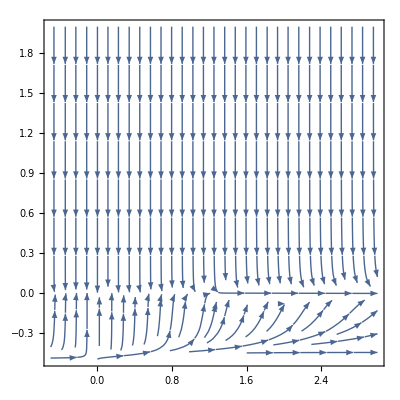

```mathematica
StreamPlot[{betaL,betaM},{lambda,-0.5,3},{mass,-0.5,2}]
```

```mathematica
DSolve[y'[t]==-a*y[t]-b*(y[t])^3,y[t],t]
```

{{y[t]→-(√a)/(√(-b+ⅇ^(2 a (t-C[1]))))},{y[t]→(√a)/(√(-b+ⅇ^(2 a (t-C[1]))))}}

```mathematica
Manipulate[Plot[(√a)/(√(-b+ⅇ^(2 a (t-c)))),{t,0,10},PlotRange->Automatic],{a,0,1},{b,0,3},{c,-5,5}]
```